{{u[t]→InterpolatingFunction[…][t],v[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t],a[t]→InterpolatingFunction[…][t]}}

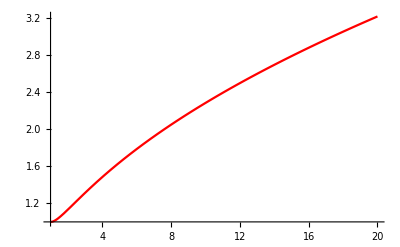

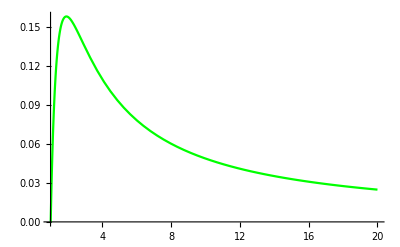

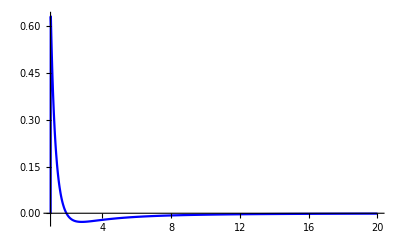

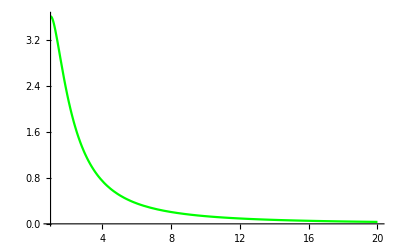

```mathematica
d=3;
(*we can change g and Subscript[ϕ, 1]*)
g=10^7;
Subscript[ϕ, 1]=0.1;
w[a_]:=2/(π*d)ArcTan[g*Log[a]];
Subscript[v, 1]=-2;

Subscript[ρ, 0]=Subscript[v, 1]^2/Exp[Subscript[ϕ, 1]];
f[a_]:=-d((1+w[a])/a)
F[a_]:=Integrate[f[a],a]
ρ[a_]:=Subscript[ρ, 0] Exp[F[a]]
p[a_]:=w[a]*ρ[a]
s=NDSolve[{
u'[t]-u[t]^2/2-(u[t]-v[t])^2/(2d)==0,
v'[t]-u[t]v[t]+Exp[ϕ[t]] ρ[a[t]]/2-1/2 Exp[ϕ[t]]p[a[t]]d==0,
ϕ'[t]-v[t]==0,
a'[t]-a[t](v[t]-u[t])/d==0,
a[1]==1,u[1]==-2,ϕ[1]==0.1,v[1]==-2},{u[t],v[t],ϕ[t],a[t]},{t,1,10000}]

(*plot a(t)*)
Case1=Plot[Evaluate[a[t]]/.s,{t,1,20},PlotRange->All,PlotStyle->Red] 
Export["/home/ketchup/cosmology/string_gas_cos/data/a_10E7.txt",Cases[Case1,Line[data_]:>data,-4,1][[1]],"Table"];


 (*plot H(t)*)
Case2=Plot[Evaluate[(v[t]-u[t])/d]/.s,{t,1,20},PlotRange->All,PlotStyle->Green]
Export["/home/ketchup/cosmology/string_gas_cos/data/H_10E7.txt",data =Cases[Case2,Line[data_]:>data,-4,1][[1]],"Table"];
f[t]=F[a[t]];

(*plot H'(t)*)
Case3=Plot[Evaluate[1/d(u[t]v[t]-(1-w[a[t]]d)Exp[ϕ[t]](1/2 Subscript[ρ, 0] Exp[f[t]])-(u[t]^2/2+(u[t]-v[t])^2/(2d)))]/.s,{t,1,20},PlotRange->All,PlotStyle->Blue]

Export["/home/ketchup/cosmology/string_gas_cos/data/H'_10E7.txt",Cases[Case3,Line[data_]:>data,-4,1][[1]],"Table"];
Export["/home/ketchup/cosmology/string_gas_cos/graph/H'_10E7.jpg", Case3];

(*plot ρ(t)*)
case4=Plot[Evaluate[Subscript[ρ, 0] Exp[f[t]]]/.s,{t,1,20}, PlotRange->All, PlotStyle->Green]
Export["/home/ketchup/cosmology/string_gas_cos/data/ρ_10E7.txt",Cases[Case3,Line[data_]:>data,-4,1][[1]],"Table"];
Export["/home/ketchup/cosmology/string_gas_cos/graph/ρ_10E7.jpg", case4];
```